```mathematica
Clear["`*"]
```

```mathematica
range={DateObject[DateValue[{"Year","Month","Day"}]],Now};
range=(UnixTime[#]*1000&)/@range;
```

```mathematica
data=Developer`ReadRawJSONString/@Import["/home/bczhc/xdo-rec/2023-03-20 12:50:37","List"]//Parallelize;
```

```mathematica
data=Select[data,range[[1]]<=#["time"]<=range[[2]]&];
```

```mathematica
plotEvent[type_]:=Module[{plotData},
plotData=FromUnixTime@#["time"]&/@Select[data,#["event"]["type"]==type&];
DateHistogram[plotData,"Hour",DateReduction->"Day"]
];
```

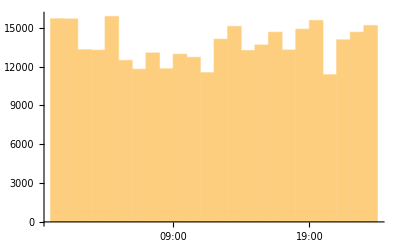

```mathematica
plotEvent["MouseMotion"]
```

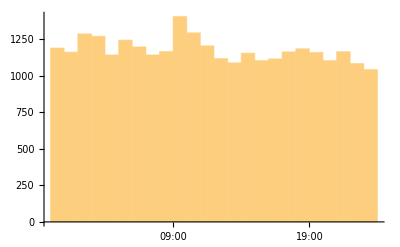

```mathematica
plotEvent["KeyPress"]
```

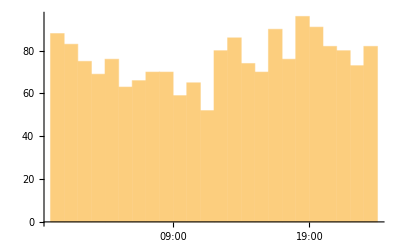

```mathematica
plotEvent["Button"]
```

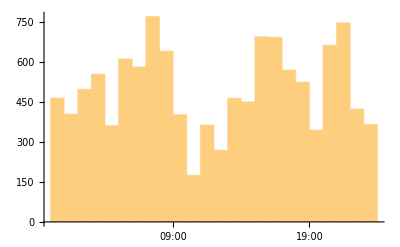

```mathematica
plotEvent["MouseWheel"]
```

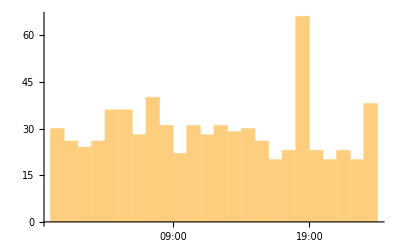

```mathematica
plotEvent["Selection"]
```

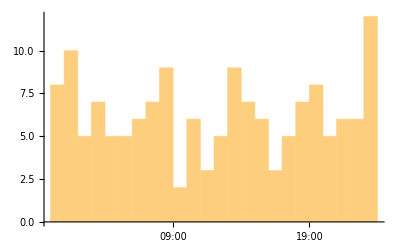

```mathematica
plotEvent["Clipboard"]
```